# BCI for Thought Recognition

## A Machine Learning approach Loading the data and formatting it appropriately: Here we are loading the data, previously filtered in Matlab, in an appropriate “Dataset”.

```mathematica
oxyYesMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/NIRSoxy_yes_signal.mat"];
numSamplesOxyYes = Dimensions[oxyYesMatlab][[3]]
oxyYesRaw =  Table[Transpose[oxyYesMatlab[[1,1,x]]],{x,numSamplesOxyYes}];


oxyNoMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/NIRSoxy_no_signal.mat"];
numSamplesOxyNo = Dimensions[oxyNoMatlab][[3]];
oxyNoRaw =  Table[Transpose[oxyNoMatlab[[1,1,x]]],{x,numSamplesOxyNo}];
```

30

```mathematica
oxyDataFullYes = Thread[Table[oxyYesRaw[[x,All,All]],{x,numSamplesOxyYes}]-> "Yes"];
oxyDataFullNo = Thread[Table[oxyNoRaw[[x,All,All]],{x,numSamplesOxyNo}]->"No"];
fullDataYesAndNo = Join[oxyDataFullNo,oxyDataFullYes];
```

```mathematica
Dimensions[oxyDataFullYes[[1]]]
```

{2}

### Check for Appropriate Loading

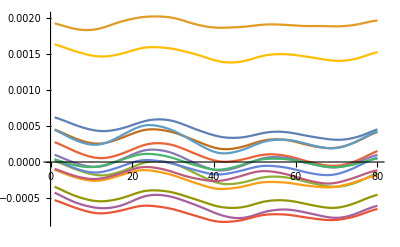

```mathematica
ListLinePlot[fullDataYesAndNo[[RandomInteger[60]]]]
```

## Division of the dataset in train and test sets

```mathematica
fracTrainTest = 0.8;
dataPoints = Length[fullDataYesAndNo]
trainPoints = Round@dataPoints*fracTrainTest;
testPoints = dataPoints-trainPoints;

trainDataYesAndNo = RandomSample[fullDataYesAndNo,trainPoints];
testDataYesAndNo = Complement[fullDataYesAndNo,trainDataYesAndNo];

Counts[Table[Values@trainDataYesAndNo[[n]],{n,trainPoints}]]
Counts[Table[Values@testDataYesAndNo[[n]],{n,testPoints}]]
```

60

<|No→23,Yes→25|>

<|Yes→5,No→7|>

```mathematica
c1 = Classify[trainDataYesAndNo]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[c1,testDataYesAndNo, "Accuracy"]
```

0.583333

```mathematica
ClassifierInformation[c1]
```

Classifier information
Number of classes | 2
Number of features | 15
Number of training examples | 20
Combination method | Geometric
Number of methods | 15
1) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 100.
2) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
3) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
4) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
5) K-nearest neighbors | Number of neighbors | 1
Distance function | EuclideanDistance
6) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
7) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
8) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
9) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
10) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 1.×10^10
11) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
12) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 100.
13) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 1.×10^10
14) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 10.
15) Logistic regression | L1 regularization coefficient | 0
L2 regularization coefficient | 100.

```mathematica
ClassifierMeasurements[c1,testDataYesAndNo,"ConfusionMatrix"]
```

{{4,0,0},{2,6,0}}

```mathematica
classifyMethods = {"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","NeuralNetwork","RandomForest","SupportVectorMachine"}
```

{LogisticRegression,Markov,NaiveBayes,NearestNeighbors,NeuralNetwork,RandomForest,SupportVectorMachine}

```mathematica
trainClassifiers =Association@@(#->  Classify[trainDataYesAndNo,PerformanceGoal->"Quality",Method->{#}]&/@classifyMethods)
```

<|LogisticRegression→ClassifierFunction[…],Markov→ClassifierFunction[…],NaiveBayes→ClassifierFunction[…],NearestNeighbors→ClassifierFunction[…],NeuralNetwork→ClassifierFunction[…],RandomForest→ClassifierFunction[…],SupportVectorMachine→ClassifierFunction[…]|>

```mathematica
Query[All,ClassifierMeasurements[#,testDataYesAndNo,"Accuracy"]&]@trainClassifiers
```

<|LogisticRegression→0.75,Markov→0.5,NaiveBayes→0.583333,NearestNeighbors→0.666667,NeuralNetwork→0.666667,RandomForest→0.5,SupportVectorMachine→0.75|>

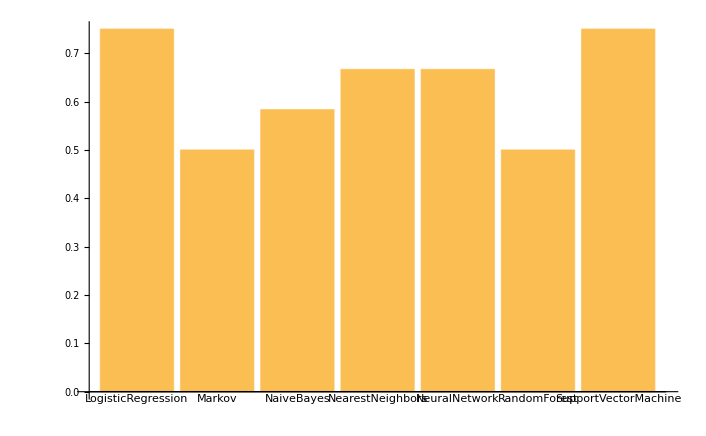

```mathematica
BarChart[%39,ChartLabels->Automatic]
```

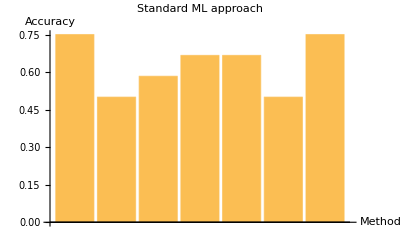

```mathematica
Show[%41,AxesLabel->{HoldForm[Method],HoldForm[Accuracy]},PlotLabel->HoldForm[Standard ML approach],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Query[1;;5,ClassifierMeasurements[#,testDataYesAndNo,"ConfusionMatrixPlot"]&]@trainClassifiers
```

Failure[…]

```mathematica
10/12
```

5/6